```mathematica
(* Gradient Descent with Independent Shifting across Each Variable

	Cycle through each parameter - factor here is instead existing for each parameter.



 *)

(* Fitting Function *)
Fitfunction=#2 ⅇ^(#3*#1)+#4&;
varamt=3;

(* Data Generation Settings *)
TrueParams={1.,0.259,1.};
DataLength=100;
SamplingRate=10;
SamplingSet=N[Range[DataLength]]/N[SamplingRate];
NoiseDistribution=NormalDistribution[];
NoiseMagnitude=0.1;

(* Data Generation *)
Noise[x_]:=x*(1.+NoiseMagnitude*RandomVariate[NoiseDistribution]);
DataNoiseless=(Fitfunction@@ #&)/@(Prepend[TrueParams, #]& /@SamplingSet);
Data=Noise/@DataNoiseless;

(*Prep gradient*)
Clear[eFunc,gFunc,params]
params=Table[Unique["p"],{varamt}];
paramh=Hold@@params;
eFunc=paramh/._[vars__]:>Function[{vars},Total[(((Fitfunction@@Prepend[{vars},#])&/@SamplingSet)-Data)^2]];
gFunc=paramh/._[vars__]:>Function[{vars},Evaluate@Grad[eFunc@@params,params]];

(* Iteration Initialization *)
factor=ConstantArray[0.05,varamt];
totalIter=0;TotalRefines=0;dir={0,0,0};
(*History*)
debugParams={iterParams=initParams={0., 1., 1.}};
```

```mathematica
(*** Iteration Settings ***)

(* Controls - zero fps means that there is NO DELAY *)
doPrint=False;doGraph=False;fps=1./5.;doWarn=False;
doPlot=True;doSpace=True;doEPlot=False;

(** Controls for limiting values **)
err=10000;(*Initialization of error. Start impossible.*)
errorRatio=1.0;(*In what ratio of current error to previous error should it be considered increasing*)
boostRatio=1.2; (*'Impatience' Multiplier to increase factor when error is not increasing*)
refineRatio=0.9;(*'Caution' Multiplier to decrease factor when error is increasing*)
maxRefines=1000;(*Give up refining if refined too many times in a row*)
SmallErr=0.001;(*Small error threshold*)

(* Tracker values *)
prevErr=-1;ConsecRefines=0;

(* Iteration Tools Extracted for Compactness *)
ReportIteration[i_]:=If[Mod[i,100]==0 && doPrint,Print["next dir:",dir,"\nerr:",err,"\nparams:",iterParams,"\niteration:",i];];
RevertParams[]:=(iterParams=debugParams[[-1]]);
ExceededMaxRefines[]:=(If[doWarn,Print["Exceeded maximum amount of consecutive corrections."]];Abort[];);
```

```mathematica
(* Realtime monitor plot *)
displayGradient[xV_,yV_]:=Show[ContourPlot[eFunc @@ ReplacePart[iterParams, {xV->x,yV->y}],
{x,iterParams[[xV]]-0.2,iterParams[[xV]]+0.2},{y,iterParams[[yV]]-0.2,iterParams[[yV]]+0.2},
PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small],
Graphics[{Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}]}]];
(* Visualization of the first 3 function parameters *)
Dynamic[Grid[{{"Data vs Function","Parameter Space","Error over iterations"},
{ListPlot[{(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,Data},Joined->True,ImageSize->Medium]
,If[varamt==3,If[doGraph,{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]},
Show[ListPointPlot3D[debugParams,PlotRange->All,ImageSize->Medium],Graphics3D@Line@debugParams],"Non-3 dimensions"]],
If[doEPlot,ListLogPlot[{((eFunc@@#)&)/@debugParams},ImageSize->Medium],"Disabled"]
},
{"Parameters, Delta","Iterations, factor, corrections"},{Column[{iterParams,-factor*dir}],Column[{{totalIter,factor,TotalRefines},ProgressIndicator[ConsecRefines/maxRefines]}],{err,prevErr}}
},Frame->All,ItemSize->30]]
```

```mathematica
(*** Iteration loop ***)

(* Iterator and maximum values *)
i=0;UpperBound=1000;

While[i<UpperBound&&err>SmallErr,

];


(* Iteration *)
While[i<UpperBound && err >SmallErr,
(* Parameters *)
For[j=1,j≤varamt,j++,
err=eFunc @@ iterParams;
(* Adaptivity: If err increased, revert, refine, and retry *)
If[err/prevErr>errorRatio,
RevertParams[];
If[ConsecRefines>maxRefines,
ExceededMaxRefines[];,
ConsecRefines++;
TotalRefines++;
factor[[j]]*=refineRatio;],
prevErr=err;
ConsecRefines=0;
debugParams=Append[debugParams,iterParams];
factor[[j]]*=boostRatio
];
dir=gFunc @@ iterParams;
iterParams-=factor*dir;
ReportIteration[i];
If[fps≠0&&ConsecRefines==0,Pause[fps];];
j++;
];
If[ConsecRefines==0,i++;];
totalIter++;
];
```

$Aborted

```mathematica
factor
dir
```

{0.000309227,0.05,0.00023192}

{7.32232×10^7,0.,0.}

-0.00334754 | 1. | 1.
-0.00334754 | 1. | 1.
-0.00334754 | 1. | 1.
-0.00334754 | 1. | 1.
-0.00334754 | 1. | 1.
-0.00334754 | 1. | 1.
-0.00334754 | 1. | 1.
-0.00334754 | 1. | 1.
-0.00334754 | 1. | 1.
-0.00334754 | 1. | 1.

80041.7
80041.7
80041.7
80041.7
80041.7
80041.7
80041.7
80041.7
80041.7
80041.7

-5.91835×10^7 | 1.96157×10^6 | 198119.
-5.91835×10^7 | 1.96157×10^6 | 198119.
-5.91835×10^7 | 1.96157×10^6 | 198119.
-5.91835×10^7 | 1.96157×10^6 | 198119.
-5.91835×10^7 | 1.96157×10^6 | 198119.
-5.91835×10^7 | 1.96157×10^6 | 198119.
-5.91835×10^7 | 1.96157×10^6 | 198119.
-5.91835×10^7 | 1.96157×10^6 | 198119.
-5.91835×10^7 | 1.96157×10^6 | 198119.
-5.91835×10^7 | 1.96157×10^6 | 198119.

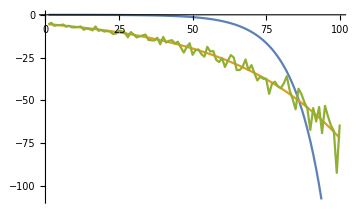

{1.76752×10^-18,0.05,1.47293×10^-18}

```mathematica
(***Diagnostic Tools***)

(*Optional Noise Function Plot*)
Plot[Noise[x],{x,0,40},AspectRatio->Full,ColorFunction->Function[{x,y},Hue[Abs[y-x]]]];

(*Parameter History*)
Grid[debugParams[[-10;;-1]]]
Column[eFunc @@ #&/@ debugParams[[-10;;-1]]]
Grid[gFunc @@ #&/@ debugParams[[-10;;-1]]]

(*"Best Parameters" Generated with NMinimize*)
AutoParams=params/.NMinimize[eFunc @@ params,params][[2]];

(*Compare current data, auto-fitted data, and generated data*)
ListPlot[{(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,(Fitfunction@@Prepend[AutoParams,#])&/@SamplingSet,Data},Joined->True,ImageSize->Medium]

factor
```

```mathematica
iterParams
```

{0.,1.,1.}

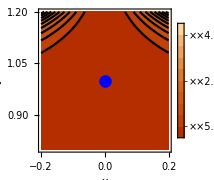
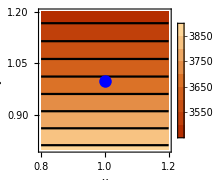
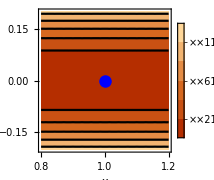

```mathematica
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]}
```

```mathematica
j
```

1